Mironova Liliya

1) Use Range, Reverse and Join to create {1, 2, 3, 4, 4, 3, 2, 1}

```mathematica
Join[Range[1,4], Reverse[Range[1,4]]]
```

{1,2,3,4,4,3,2,1}

2) M=a_ij
to calculate determinant, eigenvalues and eigenvectors for M, where a_ij is the random real numbers in the range (1, 5)

```mathematica
M = Table[RandomReal[5],{i,1,5},{j,1,5}]
Det[M]
Eigenvectors[M]
Eigenvalues[M]
```

{{2.30933,4.62382,1.95961,2.17619,3.68217},{3.63475,4.64852,1.38155,0.500066,1.78809},{3.47397,0.53693,0.668689,3.25977,4.53293},{3.70751,2.38737,4.1709,4.90903,4.67366},{3.67565,2.65145,2.04935,4.56647,3.17202}}

-320.829

{{0.406796+0. ⅈ,0.301827+0. ⅈ,0.392984+0. ⅈ,0.595635+0. ⅈ,0.483942+0. ⅈ},{0.275675+0. ⅈ,0.69261+0. ⅈ,-0.351355+0. ⅈ,-0.526137+0. ⅈ,-0.209819+0. ⅈ},{0.707683+0. ⅈ,-0.19905+0. ⅈ,-0.379015+0. ⅈ,0.261047+0. ⅈ,-0.49776+0. ⅈ},{0.147057+0.0435856 ⅈ,-0.1607-0.16449 ⅈ,0.684096+0. ⅈ,-0.347165-0.36942 ⅈ,-0.106206+0.432818 ⅈ},{0.147057-0.0435856 ⅈ,-0.1607+0.16449 ⅈ,0.684096+0. ⅈ,-0.347165+0.36942 ⅈ,-0.106206-0.432818 ⅈ}}

{15.2+0. ⅈ,4.47284+0. ⅈ,-1.82789+0. ⅈ,-1.06866+1.19984 ⅈ,-1.06866-1.19984 ⅈ}

3) Plot all roots of the equation (∑_(i=0))^10(-1)^i/(i !)x^i=0 on the complex plane
(as result to provide exported file)

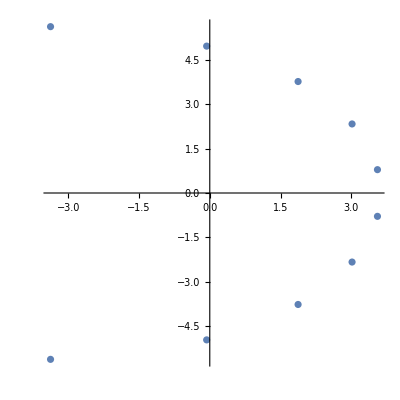

```mathematica
FigRandomPoly=Block[{eq,sol,n=10,real,image},
eq=Sum[(-1)^i / Factorial[i]x^i,{i,0,n}];
sol=x/.Solve[eq==0,x];
real=Re[sol];
image=Im[sol];
ListPlot[Table[{real[[i]],image[[i]]},{i,1,n}],AspectRatio->1]
]
```

4) Using ContourPlot[] and Manipulate[] to estimate R which provides exactly 2 solution of the following system

x^2+y^2=R^2
x y=1

```mathematica
Manipulate[
ContourPlot[{x^2+y^2==R^2, x y ==1},{x,-2,2},{y,-2,2}],
{R,0,5,0.1}
]
```

R = 1.4